```mathematica
"exercicios da aula 3"

list1 = Range[4]
```

exercicios da aula 3

{1,2,3,4}

```mathematica
list2 = Range[100]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}

```mathematica
list3 = Reverse[Range[4]]
```

{4,3,2,1}

```mathematica
list4 = Reverse[Range[50]]
```

{50,49,48,47,46,45,44,43,42,41,40,39,38,37,36,35,34,33,32,31,30,29,28,27,26,25,24,23,22,21,20,19,18,17,16,15,14,13,12,11,10,9,8,7,6,5,4,3,2,1}

```mathematica
list5 = Join[Range[4], Reverse[Range[4]]]
```

{1,2,3,4,4,3,2,1}

```mathematica
list6 = Join[Range[100], Reverse[Range[99]]];
ListLinePlot[list6]
```

-Graphics-

```mathematica
randomLength = RandomInteger[{1, 10}];
list7 = Range[randomLength]
```

{1,2,3,4,5,6,7,8}

```mathematica
simplerForm8 = Range[10]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
simplerForm9 = Join[{1, 2}, {3, 4}, {5}]
```

{1,2,3,4,5}

```mathematica
simplerForm10 = Join[Range[10], Range[10], Range[5]]
```

{1,2,3,4,5,6,7,8,9,10,1,2,3,4,5,6,7,8,9,10,1,2,3,4,5}

```mathematica
simplerForm11 = Join[Reverse[Range[20]], Range[20]]
```

{20,19,18,17,16,15,14,13,12,11,10,9,8,7,6,5,4,3,2,1,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20}

Exercícios aula 4

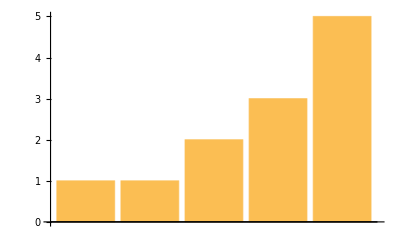

```mathematica
"Exercícios aula 4"


BarChart[{1, 1, 2, 3, 5}]
```

```mathematica
PieChart[Range[10]]
```

-Graphics-

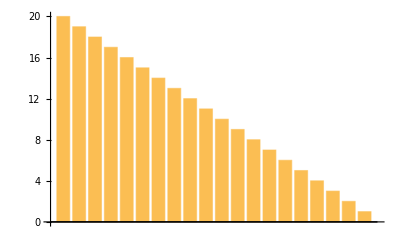

```mathematica
BarChart[Reverse[Range[20]]]
```

```mathematica
Column[Range[5]]
```

1
2
3
4
5

```mathematica
ListLinePlot[{1, 4, 9, 16, 25}]
```

-Graphics-

```mathematica
PieChart[ConstantArray[1, 10]]
```

-Graphics-

```mathematica
Column[{
  PieChart[ConstantArray[1, 1]],
  PieChart[ConstantArray[1, 2]],
  PieChart[ConstantArray[1, 3]]
}]
```

-Graphics-